# Loop Equations Bootstrap

Okay, a little introduction to what we’re trying to do. This code generates the figures for section 4 — Bootstrapping 1-matrix models. For simplicity, we start with the single Hermitian matrix model:

V(ϕ)=1/2 ϕ^2+ 1/4 g ϕ^4

This is page 7 in the paper, equation 4.14. From that same page:

“We will take the search space S to be a single parameter t_2≥ 0 and set all odd correlation functions to zero.”

We follow the general approach outlined above to derive constraints. In other words:

- starting from some value of t_2, we use the loop equations to compute all correlations up to some power 2d
- We assemble these correlators into the inner product matrix M_dxd,
- and find the region where all its eigenvalues are positive.

### some analytics

I guess these are set up for later analytics, whatever that means. The first line is identical what

```mathematica
c2[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/3 a^2(4-a^2)];
c2[0]=1;
c4[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/2 a^4(6-2a^2)];
c2p[x_]:=1-2 x+9 x^2-54 x^3;
c4p[x_]:=2-9 x+54 x^2-378 x^3;
```

```mathematica
ρ[g_,λ_]:=Module[{a2=2/(3 g)(-1+Sqrt[1+12 g])},-I/(2π)(g λ^2+g a2/2+1)Sqrt[λ^2-a2] ]
```

### A view of the peninsula

Okay, getting better at this. We want to do a view of the peninsula. So, clear things up... here we use the loop equations to calculate all of the correlators?

```mathematica
Clear[g]; Remove[t];
```

I go through this more clearly later, but here’s a nice example.

```mathematica
Subscript[t, 0]=1;Subscript[t, 1] = 0;max=71;(*Odd number*)
```

This is the equation of motion that we get, that, because we’ve set t_1 = 0, has all even terms equal to 0. No need to special case, as they’ll all drop out.

```mathematica
Do[Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[0,max]}];
expressions=Table[ Evaluate[ Subscript[t, k]],{k,Range[1,max+1]} ];
tk=expressions[[-21]];
tk1=expressions[[-11]];
tk2=expressions[[-1]];
```

This is equivalent to actually printing the simplified value of t_4:

```mathematica
expressions[[4]]
```

(1-t_2)/g

I’ve goofed these indices, so we’re now actually calculating ALL of the stuff, except that t_1=0 gets a lot of it to simplify out from the beginning.

NOTES on the sum:
* We have this nice property that if you set t_1=0, all of the odd terms become 0, all the way up. Why? Well, look at the summation. If k is even (which means, somehow, that we’re calculating the EVEN traces...), then k-1 is odd... odd + even = odd, even + odd = odd, so you’ll always have an odd term in every element of the summation.

Since you build up from t_1, all of those terms cancel, as does the t_(k+1), also odd when k is even.

See the blog notes for why you can write the loop equation recursive definition of the correlators in this way.

```mathematica
Information[tk]Sin[1/2]
```

```mathematica
p0=Plot[{Solve[tk==0][[1,1,2]],Solve[tk==0][[2,1,2]]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0]},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
p1=Plot[{Solve[tk1==0][[1,1,2]],Solve[tk1==0][[2,1,2]]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0]},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
p2=Plot[{Solve[tk2==0][[1,1,2]],Solve[tk2==0][[2,1,2]],c2[g]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0],{Darker@Green,Thickness[0.004]}},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
gg=Show[p0,p1,p2];
Labeled[gg,{"tr M^2","g"},{Left,Bottom},labelsci]
```

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[{Solve[tk==0]⟦1,1,2⟧,Solve[tk==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[{Solve[tk1==0]⟦1,1,2⟧,Solve[tk1==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[{Solve[tk2==0]⟦1,1,2⟧,Solve[tk2==0]⟦2,1,2⟧,c2[g]},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0],{Darker[Green],Thickness[0.004]}},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Solve[tk==0]⟦1,1,2⟧,Solve[tk==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}],Plot[{Solve[tk1==0]⟦1,1,2⟧,Solve[tk1==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}],Plot[{Solve[tk2==0]⟦1,1,2⟧,Solve[tk2==0]⟦2,1,2⟧,c2[g]},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0],{Darker[Green],Thickness[0.004]}},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}]].

Labeled[Show[Plot[{Solve[tk==0]⟦1,1,2⟧,Solve[tk==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}],Plot[{Solve[tk1==0]⟦1,1,2⟧,Solve[tk1==0]⟦2,1,2⟧},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0]},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}],Plot[{Solve[tk2==0]⟦1,1,2⟧,Solve[tk2==0]⟦2,1,2⟧,c2[g]},{g,-0.09,0},PlotPoints→200,PlotRange→{0.9,3},PlotStyle→{Opacity[0],Opacity[0],{Darker[Green],Thickness[0.004]}},plotsci,Filling→{1→{2}},FillingStyle→{Opacity[0.15],Gray}]],{tr M^2,g},{Left,Bottom},labelsci]

```mathematica
Manipulate[Plot[tk2/.{g->gg},{Subscript[t, 2],0,1.5}],{gg,-0.08,1.0}]
```

```mathematica
tk2/.{g->3.0,Subscript[t, 2]->0.7}
```

9.45694

```mathematica
Expand[(X-a)^4]
```

a^4-4 a^3 X+6 a^2 X^2-4 a X^3+X^4

```mathematica
m={{Subscript[t, 2j],Subscript[t, j+k]},{Subscript[t, j+k],Subscript[t, 2k]}}
```

{{t_(2 j),t_(j+k)},{t_(j+k),t_(2 k)}}

```mathematica
Eigenvalues[m]//FullSimplify
```

{1/2 (t_(2 j)+t_(2 k)-√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2)),1/2 (t_(2 j)+t_(2 k)+√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2))}

```mathematica
1/4 (1+x2m-√(1-2 x2m+x2m^2+4 xm^2))^2//Expand
```

1/2+x2m^2/2+xm^2-1/2 √(1-2 x2m+x2m^2+4 xm^2)-1/2 x2m √(1-2 x2m+x2m^2+4 xm^2)

#### Fingers plot

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=71;(*Odd number*)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
expressions=Table[ Evaluate[ Subscript[t, k]],{k,Range[2,max+1,2]} ];
tk2=expressions[[-1]];
tk22=expressions[[-3]];
```

```mathematica
tk6=expressions[[4]];
```

```mathematica
p=Plot[{Solve[tk22==0][[;;,1,2]],c2[g]},{g,-0.08,2.5},PerformanceGoal->"Quality",PlotRange->{0,2}, Evaluate@plotsci,PlotStyle->{Black,{Darker@Green,Dashed}},Filling->{4->{2}}]
```

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[{Solve[tk22==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Black,{Darker[Green],Dashed}},Filling→{4→{2}}]. An option must be a rule or a list of rules.

Plot[{Solve[tk22==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Black,{Darker[Green],Dashed}},Filling→{4→{2}}]

```mathematica
Show[p,AspectRatio-> 0.6180339887498948]
```

Show::gtype: Plot is not a type of graphics.

Show[Plot[{Solve[tk22==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Black,{Darker[Green],Dashed}},Filling→{4→{2}}],AspectRatio→0.618034]

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

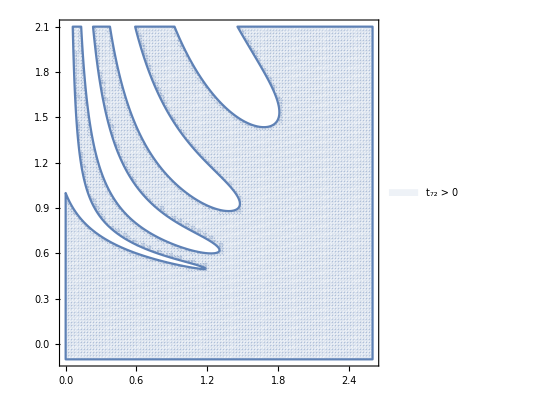

```mathematica
rp72=RegionPlot[{tk2>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_72 > 0","t_68 > 0","t_8 > 0"},PlotStyle->Opacity[0.1]]
```

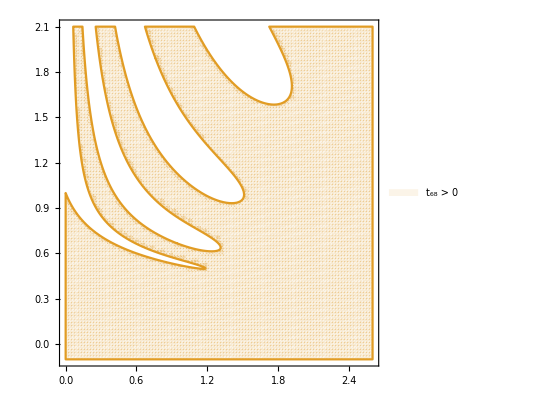

```mathematica
rp68=RegionPlot[{tk22>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_68 > 0","t_8 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Opacity[0.1]]},BoundaryStyle->ColorData[97,"ColorList"][[2]]
]
```

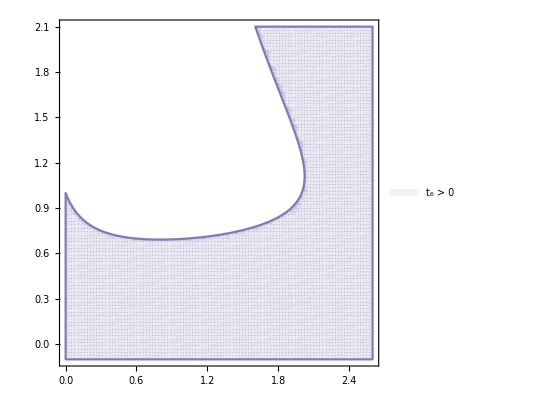

```mathematica
rp6=RegionPlot[{tk6>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_6 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],Opacity[0.1]]},BoundaryStyle->ColorData[97,"ColorList"][[5]]
]
```

Show::gcomb: Could not combine the graphics objects in ….

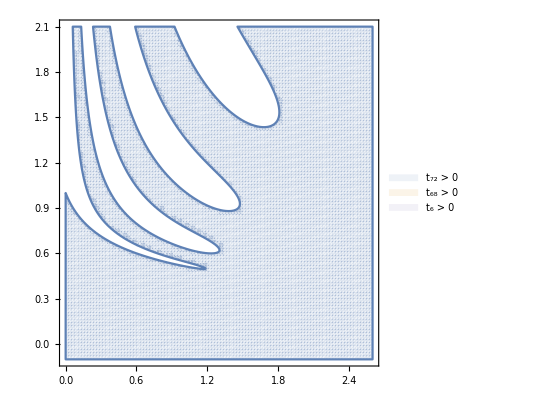
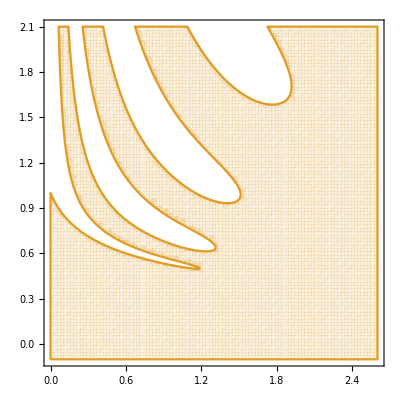
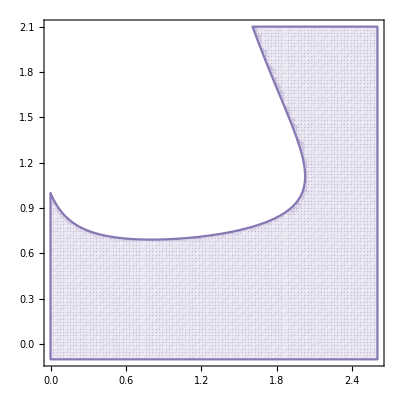
Labeled[Show[-Graphics-,-Graphics-,-Graphics-,exact,PlotRange→{{0.05,2.5},{0,2.}},plotsci,AspectRatio→0.618034],tr M^2,Left,labelsci]

```mathematica
Labeled[Show[rp72,rp68,rp6,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948],"tr M^2",Left,labelsci]
```

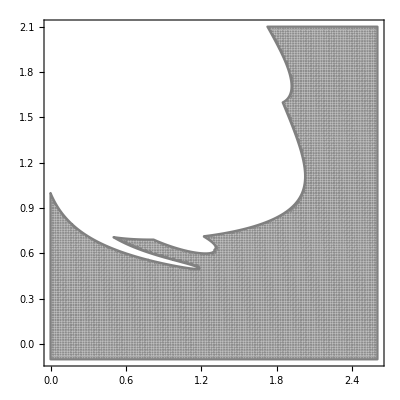

```mathematica
rpInt=RegionPlot[{tk2>0&&tk6>0&&tk22>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->200,PlotStyle->{Opacity[0.3],Gray},BoundaryStyle->Gray]
```

```mathematica
Labeled[Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948],{"tr M^2","g"},{Left,Bottom},labelsci]
```

Show::gcomb: Could not combine the graphics objects in ….

Labeled[Show[-Graphics-,exact,PlotRange→{{0.05,2.5},{0,2.}},plotsci,AspectRatio→0.618034],{tr M^2,g},{Left,Bottom},labelsci]

```mathematica
Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,exact,PlotRange→{{0.05,2.5},{0,2.}},plotsci,AspectRatio→0.618034]

```mathematica
Show[rp72,rp68,rp6,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,-Graphics-,exact,PlotRange→{{0.05,2.5},{0,2.}},plotsci,AspectRatio→0.618034]

```mathematica
exact=Plot[c2[g],{g,-0.08,2.6},PerformanceGoal->"Quality",PlotRange->{0,2}, Evaluate@plotsci,PlotStyle->{Thick,Black},Filling->{4->{2}}]
```

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[c2[g],{g,-0.08,2.6},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Thick,Black},Filling→{4→{2}}]. An option must be a rule or a list of rules.

Plot[c2[g],{g,-0.08,2.6},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Thick,Black},Filling→{4→{2}}]

```mathematica
Labeled[p,{"tr M^2","g" },{Left,Bottom},labelsci]
```

Plot::nonopt: Options expected (instead of plotsci) beyond position 2 in Plot[{Solve[tk22==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Black,{Darker[Green],Dashed}},Filling→{4→{2}}]. An option must be a rule or a list of rules.

Labeled[Plot[{Solve[tk22==0]⟦1;;All,1,2⟧,c2[g]},{g,-0.08,2.5},PerformanceGoal→Quality,PlotRange→{0,2},plotsci,PlotStyle→{Black,{Darker[Green],Dashed}},Filling→{4→{2}}],{tr M^2,g},{Left,Bottom},labelsci]

#### Fancy method

here we do max =10, for just the negative part.

```mathematica
Subscript[t, 0]=1;
Subscript[t, 1]=0;
max=14; (* choose an even number for compatibility with cM *)
(** in this code, Subscript[t, 2] is left as the variable **)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max-3,2]}];
```

```mathematica
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
res=1/400;
dat2=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,-34,-1}];
down2=Transpose@{dat2[[;;,1]],dat2[[;;,2,5]]};
up2=Transpose@{dat2[[;;,1]],dat2[[;;,2,6]]};
down0={{0,1}};
up0={{0,1}};
downn=Sort@Join[down0,down2];
upp=Sort@Join[up0,up2];
(* dat=Delete[dat,3];*)
```

Show::gcomb: Could not combine the graphics objects in ….

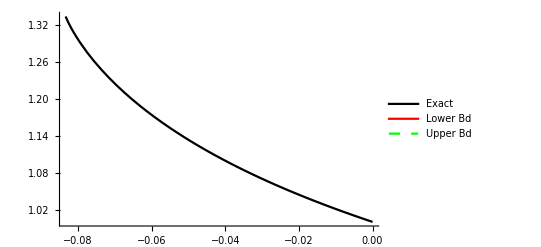
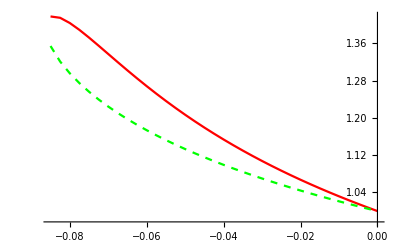
Labeled[Show[-Graphics-,-Graphics-,plotsci],{⟨Tr M^2⟩,g},{Left,Bottom},labelsci]

```mathematica
Labeled[Show[Plot[{c2[x]},{x,-1/10,0},PlotStyle->{Black},PlotLegends->{"Exact"},GridLines->{{0,-1/12}},PlotRange->All ],ListPlot[{upp,downn},Joined->True,InterpolationOrder->1,PlotStyle->{Red,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"⟨Tr M^2⟩","g"},{Left,Bottom},labelsci]
```

here we do max=20.

```mathematica
Subscript[t, 0]=1;
Subscript[t, 1]=0;
max=20; (* choose an even number for compatibility with cM *)
(** in this code, Subscript[t, 2] is left as the variable **)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max-3,2]}];
```

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=2;
res=1/50;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
res=1/200;
dat2=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,-20,-1}];
(* dat=Delete[dat,3];*)
```

```mathematica
up=Transpose@{dat[[;;,1]],dat[[;;,2,9]]};
down=Transpose@{dat[[;;,1]],dat[[;;,2,8]]};
up2=Transpose@{dat2[[;;,1]],dat2[[;;,2,8]]};
down2=Transpose@{dat2[[;;,1]],dat2[[;;,2,7]]};
down0={{0,1}};
up0={{0,1}};
upp=Sort@Join[up,up0,up2];
downn=Sort@Join[down,down0,down2];
```

```mathematica
exact={#,N[c2@#]}&/@upp[[;;,1]];
```

```mathematica
exact[[2]]
```

{-19/200,1.45686-0.107486 ⅈ}

```mathematica
upperr=Table[{exact[[i,1]],upp[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
downerr=Table[{exact[[i,1]],downn[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
```

Show::gcomb: Could not combine the graphics objects in ….

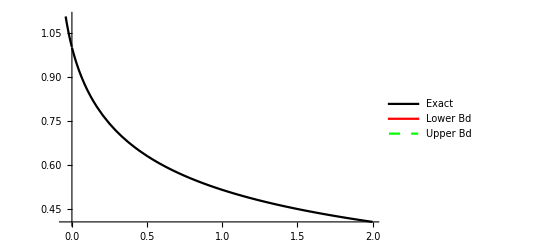
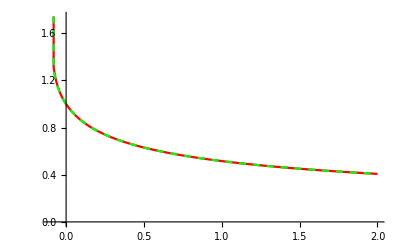
Labeled[Show[-Graphics-,-Graphics-,plotsci],{⟨Tr M^2⟩,g},{Left,Bottom},labelsci]

```mathematica
Labeled[Show[Plot[{c2[x]},{x,-1/24,2},PlotStyle->{Black},PlotLegends->{"Exact"},GridLines->{{0,-1/12}}],ListPlot[{upp,downn},Joined->True,PlotStyle->{Red,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"⟨Tr M^2⟩","g"},{Left,Bottom},labelsci]
```

Nice plots

```mathematica
jm=5;res=1/100;
```

```mathematica
d=4;
dat6=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

Part::partd: Part specification dat7⟦1,2⟧ is longer than depth of object.

PrependTo::rvalue: dat7 is not a variable with a value, so its value cannot be changed.

```mathematica
d=5;
dat7=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

```mathematica
d=6;
dat8=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat8,{0,ConstantArray[1,Length[dat8[[1,2]]]]}];
```

```mathematica
up6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-1]]};
down6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-2]]};
l6=ListPlot[{down6,up6},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.3]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

ListPlot::nonopt: Options expected (instead of plotsci) beyond position 1 in ListPlot[{{{1/100,0.980762},{1/50,0.962912},{3/100,0.946274},{1/25,0.930703},{1/20,0.91608},{3/50,0.902302},{7/100,0.889284},{2/25,0.876953},{9/100,0.865244},{1/10,0.854102},{11/100,0.843479},{3/25,0.833333},{13/100,0.823626},{7/50,0.814325},«23»,{19/50,0.664457},{39/100,0.660114},{2/5,0.655869},{41/100,0.651717},{21/50,0.647656},{43/100,0.643681},{11/25,0.639789},{9/20,0.635978},{23/50,0.632245},{47/100,0.628586},{12/25,0.625},{49/100,0.621483},{1/2,0.618034},«450»},{«1»}},«7»]. An option must be a rule or a list of rules.

ListPlot[{{{1/100,0.980762},{1/50,0.962912},{3/100,0.946274},{1/25,0.930703},{1/20,0.91608},{3/50,0.902302},{7/100,0.889284},{2/25,0.876953},{9/100,0.865244},{1/10,0.854102},{11/100,0.843479},{3/25,0.833333},{13/100,0.823626},{7/50,0.814325},{3/20,0.805399},{4/25,0.796823},{17/100,0.788572},{9/50,0.780625},{19/100,0.772962},{1/5,0.765564},{21/100,0.758417},{11/50,0.751505},{23/100,0.744815},{6/25,0.738334},{1/4,0.732051},{13/50,0.725955},{27/100,0.720036},{7/25,0.714286},{29/100,0.708695},{3/10,0.703257},{31/100,0.697964},{8/25,0.69281},{33/100,0.687787},{17/50,0.68289},{7/20,0.678113},{9/25,0.673452},{37/100,0.668902},{19/50,0.664457},{39/100,0.660114},{2/5,0.655869},{41/100,0.651717},{21/50,0.647656},{43/100,0.643681},{11/25,0.639789},{9/20,0.635978},{23/50,0.632245},{47/100,0.628586},{12/25,0.625},{49/100,0.621483},{1/2,0.618034},{51/100,0.61465},{13/25,0.611329},{53/100,0.608068},{27/50,0.604867},{11/20,0.601723},{14/25,0.598634},{57/100,0.595599},{29/50,0.592616},{59/100,0.589683},{3/5,0.5868},{61/100,0.583964},{31/50,0.581174},{63/100,0.578429},{16/25,0.575728},{13/20,0.573069},{33/50,0.570452},{67/100,0.567875},{17/25,0.565337},{69/100,0.562837},{7/10,0.560374},{71/100,0.557947},{18/25,0.555556},{73/100,0.553198},{37/50,0.550875},{3/4,0.548584},{19/25,0.546325},{77/100,0.544097},{39/50,0.541899},{79/100,0.539731},{4/5,0.537592},{81/100,0.535481},{41/50,0.533398},{83/100,0.531342},{21/25,0.529312},{17/20,0.527308},{43/50,0.52533},{87/100,0.523376},{22/25,0.521446},{89/100,0.51954},{9/10,0.517657},{91/100,0.515796},{23/25,0.513958},{93/100,0.512142},{47/50,0.510347},{19/20,0.508573},{24/25,0.506819},{97/100,0.505085},{49/50,0.503371},{99/100,0.501676},{1,0.5},{101/100,0.498343},{51/50,0.496703},{103/100,0.495082},{26/25,0.493478},{21/20,0.491891},{53/50,0.490321},{107/100,0.488768},{27/25,0.48723},{109/100,0.485709},{11/10,0.484203},{111/100,0.482713},{28/25,0.481238},{113/100,0.479778},{57/50,0.478332},{23/20,0.476901},{29/25,0.475484},{117/100,0.47408},{59/50,0.47269},{119/100,0.471314},{6/5,0.469951},{121/100,0.468601},{61/50,0.467263},{123/100,0.465938},{31/25,0.464625},{5/4,0.463325},{63/50,0.462036},{127/100,0.46076},{32/25,0.459494},{129/100,0.45824},{13/10,0.456998},{131/100,0.455766},{33/25,0.454545},{133/100,0.453335},{67/50,0.452136},{27/20,0.450947},{34/25,0.449768},{137/100,0.448599},{69/50,0.44744},{139/100,0.446291},{7/5,0.445152},{141/100,0.444022},{71/50,0.442901},{143/100,0.44179},{36/25,0.440688},{29/20,0.439594},{73/50,0.43851},{147/100,0.437434},{37/25,0.436367},{149/100,0.435309},{3/2,0.434259},{151/100,0.433217},{38/25,0.432183},{153/100,0.431157},{77/50,0.430139},{31/20,0.429129},{39/25,0.428127},{157/100,0.427132},{79/50,0.426145},{159/100,0.425165},{8/5,0.424193},{161/100,0.423228},{81/50,0.42227},{163/100,0.421319},{41/25,0.420375},{33/20,0.419438},{83/50,0.418507},{167/100,0.417584},{42/25,0.416667},{169/100,0.415756},{17/10,0.414852},{171/100,0.413955},{43/25,0.413063},{173/100,0.412178},{87/50,0.411299},{7/4,0.410426},{44/25,0.409559},{177/100,0.408698},{89/50,0.407843},{179/100,0.406994},{9/5,0.40615},{181/100,0.405313},{91/50,0.40448},{183/100,0.403654},{46/25,0.402832},{37/20,0.402016},{93/50,0.401206},{187/100,0.400401},{47/25,0.399601},{189/100,0.398806},{19/10,0.398016},{191/100,0.397231},{48/25,0.396452},{193/100,0.395677},{97/50,0.394907},{39/20,0.394142},{49/25,0.393382},{197/100,0.392627},{99/50,0.391876},{199/100,0.39113},{2,0.390388},{201/100,0.389651},{101/50,0.388919},{203/100,0.388191},{51/25,0.387467},{41/20,0.386748},{103/50,0.386033},{207/100,0.385322},{52/25,0.384615},{209/100,0.383913},{21/10,0.383215},{211/100,0.382521},{53/25,0.381831},{213/100,0.381145},{107/50,0.380463},{43/20,0.379784},{54/25,0.37911},{217/100,0.37844},{109/50,0.377773},{219/100,0.37711},{11/5,0.376451},{221/100,0.375796},{111/50,0.375144},{223/100,0.374496},{56/25,0.373852},{9/4,0.373211},{113/50,0.372574},{227/100,0.37194},{57/25,0.371309},{229/100,0.370683},{23/10,0.370059},{231/100,0.369439},{58/25,0.368822},{233/100,0.368209},{117/50,0.367598},{47/20,0.366991},{59/25,0.366388},{237/100,0.365787},{119/50,0.36519},{239/100,0.364595},{12/5,0.364004},{241/100,0.363416},{121/50,0.362831},{243/100,0.362249},{61/25,0.36167},{49/20,0.361094},{123/50,0.360521},{247/100,0.359951},{62/25,0.359384},{249/100,0.358819},{5/2,0.358258},{251/100,0.357699},{63/25,0.357143},{253/100,0.35659},{127/50,0.356039},{51/20,0.355492},{64/25,0.354946},{257/100,0.354404},{129/50,0.353864},{259/100,0.353327},{13/5,0.352793},{261/100,0.352261},{131/50,0.351732},{263/100,0.351205},{66/25,0.350681},{53/20,0.350159},{133/50,0.34964},{267/100,0.349123},{67/25,0.348609},{269/100,0.348097},{27/10,0.347588},{271/100,0.34708},{68/25,0.346576},{273/100,0.346073},{137/50,0.345573},{11/4,0.345076},{69/25,0.34458},{277/100,0.344087},{139/50,0.343596},{279/100,0.343107},{14/5,0.342621},{281/100,0.342137},{141/50,0.341655},{283/100,0.341175},{71/25,0.340697},{57/20,0.340221},{143/50,0.339748},{287/100,0.339277},{72/25,0.338807},{289/100,0.33834},{29/10,0.337875},{291/100,0.337412},{73/25,0.336951},{293/100,0.336492},{147/50,0.336035},{59/20,0.33558},{74/25,0.335126},{297/100,0.334675},{149/50,0.334226},{299/100,0.333779},{3,0.333333},{301/100,0.33289},{151/50,0.332448},{303/100,0.332008},{76/25,0.331571},{61/20,0.331135},{153/50,0.3307},{307/100,0.330268},{77/25,0.329837},{309/100,0.329408},{31/10,0.328981},{311/100,0.328556},{78/25,0.328133},{313/100,0.327711},{157/50,0.327291},{63/20,0.326873},{79/25,0.326456},{317/100,0.326041},{159/50,0.325628},{319/100,0.325216},{16/5,0.324806},{321/100,0.324398},{161/50,0.323991},{323/100,0.323586},{81/25,0.323183},{13/4,0.322781},{163/50,0.322381},{327/100,0.321982},{82/25,0.321585},{329/100,0.321189},{33/10,0.320796},{331/100,0.320403},{83/25,0.320012},{333/100,0.319623},{167/50,0.319235},{67/20,0.318849},{84/25,0.318464},{337/100,0.31808},{169/50,0.317698},{339/100,0.317318},{17/5,0.316939},{341/100,0.316561},{171/50,0.316185},{343/100,0.31581},{86/25,0.315437},{69/20,0.315065},{173/50,0.314694},{347/100,0.314325},{87/25,0.313958},{349/100,0.313591},{7/2,0.313226},{351/100,0.312862},{88/25,0.3125},{353/100,0.312139},{177/50,0.311779},{71/20,0.311421},{89/25,0.311064},{357/100,0.310708},{179/50,0.310354},{359/100,0.31},{18/5,0.309648},{361/100,0.309298},{181/50,0.308948},{363/100,0.3086},{91/25,0.308253},{73/20,0.307908},{183/50,0.307563},{367/100,0.30722},{92/25,0.306878},{369/100,0.306537},{37/10,0.306198},{371/100,0.305859},{93/25,0.305522},{373/100,0.305186},{187/50,0.304851},{15/4,0.304518},{94/25,0.304185},{377/100,0.303854},{189/50,0.303524},{379/100,0.303194},{19/5,0.302866},{381/100,0.30254},{191/50,0.302214},{383/100,0.301889},{96/25,0.301566},{77/20,0.301243},{193/50,0.300922},{387/100,0.300602},{97/25,0.300283},{389/100,0.299965},{39/10,0.299648},{391/100,0.299332},{98/25,0.299017},{393/100,0.298703},{197/50,0.29839},{79/20,0.298079},{99/25,0.297768},{397/100,0.297458},{199/50,0.297149},{399/100,0.296842},{4,0.296535},{401/100,0.29623},{201/50,0.295925},{403/100,0.295621},{101/25,0.295319},{81/20,0.295017},{203/50,0.294716},{407/100,0.294416},{102/25,0.294118},{409/100,0.29382},{41/10,0.293523},{411/100,0.293227},{103/25,0.292932},{413/100,0.292638},{207/50,0.292345},{83/20,0.292053},{104/25,0.291762},{417/100,0.291471},{209/50,0.291182},{419/100,0.290893},{21/5,0.290606},{421/100,0.290319},{211/50,0.290033},{423/100,0.289748},{106/25,0.289464},{17/4,0.289181},{213/50,0.288899},{427/100,0.288617},{107/25,0.288337},{429/100,0.288057},{43/10,0.287778},{431/100,0.287501},{108/25,0.287223},{433/100,0.286947},{217/50,0.286672},{87/20,0.286397},{109/25,0.286123},{437/100,0.28585},{219/50,0.285578},{439/100,0.285307},{22/5,0.285037},{441/100,0.284767},{221/50,0.284498},{443/100,0.28423},{111/25,0.283963},{89/20,0.283696},{223/50,0.283431},{447/100,0.283166},{112/25,0.282902},{449/100,0.282638},{9/2,0.282376},{451/100,0.282114},{113/25,0.281853},{453/100,0.281593},{227/50,0.281333},{91/20,0.281074},{114/25,0.280816},{457/100,0.280559},{229/50,0.280303},{459/100,0.280047},{23/5,0.279792},{461/100,0.279538},{231/50,0.279284},{463/100,0.279031},{116/25,0.278779},{93/20,0.278528},{233/50,0.278277},{467/100,0.278027},{117/25,0.277778},{469/100,0.277529},{47/10,0.277281},{471/100,0.277034},{118/25,0.276788},{473/100,0.276542},{237/50,0.276297},{19/4,0.276053},{119/25,0.275809},{477/100,0.275566},{239/50,0.275323},{479/100,0.275082},{24/5,0.274841},{481/100,0.2746},{241/50,0.274361},{483/100,0.274122},{121/25,0.273883},{97/20,0.273646},{243/50,0.273409},{487/100,0.273172},{122/25,0.272936},{489/100,0.272701},{49/10,0.272467},{491/100,0.272233},{123/25,0.272},{493/100,0.271767},{247/50,0.271535},{99/20,0.271304},{124/25,0.271073},{497/100,0.270843},{249/50,0.270613},{499/100,0.270384},{5,0.270156}},{{1/100,0.990195},{1/50,0.980762},{3/100,0.971675},{1/25,0.962912},{1/20,0.954451},{3/50,0.946274},{7/100,0.938363},{2/25,0.930703},{9/100,0.92328},{1/10,0.91608},{11/100,0.909091},{3/25,0.902302},{13/100,0.895703},{7/50,0.889284},{3/20,0.883037},{4/25,0.876953},{17/100,0.871024},{9/50,0.865244},{19/100,0.859605},{1/5,0.854102},{21/100,0.848729},{11/50,0.843479},{23/100,0.838349},{6/25,0.833333},{1/4,0.828427},{13/50,0.823626},{27/100,0.818927},{7/25,0.814325},{29/100,0.809817},{3/10,0.805399},{31/100,0.801069},{8/25,0.796823},{33/100,0.792659},{17/50,0.788572},{7/20,0.784562},{9/25,0.780625},{37/100,0.776759},{19/50,0.772962},{39/100,0.769231},{2/5,0.765564},{41/100,0.761961},{21/50,0.758417},{43/100,0.754933},{11/25,0.751505},{9/20,0.748133},{23/50,0.744815},{47/100,0.741549},{12/25,0.738334},{49/100,0.735168},{1/2,0.732051},{51/100,0.72898},{13/25,0.725955},{53/100,0.722974},{27/50,0.720036},{11/20,0.71714},{14/25,0.714286},{57/100,0.711471},{29/50,0.708695},{59/100,0.705958},{3/5,0.703257},{61/100,0.700593},{31/50,0.697964},{63/100,0.69537},{16/25,0.69281},{13/20,0.690282},{33/50,0.687787},{67/100,0.685323},{17/25,0.68289},{69/100,0.680487},{7/10,0.678113},{71/100,0.675769},{18/25,0.673452},{73/100,0.671164},{37/50,0.668902},{3/4,0.666667},{19/25,0.664457},{77/100,0.662273},{39/50,0.660114},{79/100,0.65798},{4/5,0.655869},{81/100,0.653781},{41/50,0.651717},{83/100,0.649675},{21/25,0.647656},{17/20,0.645657},{43/50,0.643681},{87/100,0.641725},{22/25,0.639789},{89/100,0.637874},{9/10,0.635978},{91/100,0.634102},{23/25,0.632245},{93/100,0.630407},{47/50,0.628586},{19/20,0.626784},{24/25,0.625},{97/100,0.623233},{49/50,0.621483},{99/100,0.61975},{1,0.618034},{101/100,0.616334},{51/50,0.61465},{103/100,0.612981},{26/25,0.611329},{21/20,0.609691},{53/50,0.608068},{107/100,0.60646},{27/25,0.604867},{109/100,0.603288},{11/10,0.601723},{111/100,0.600172},{28/25,0.598634},{113/100,0.59711},{57/50,0.595599},{23/20,0.594101},{29/25,0.592616},{117/100,0.591143},{59/50,0.589683},{119/100,0.588235},{6/5,0.5868},{121/100,0.585376},{61/50,0.583964},{123/100,0.582563},{31/25,0.581174},{5/4,0.579796},{63/50,0.578429},{127/100,0.577073},{32/25,0.575728},{129/100,0.574393},{13/10,0.573069},{131/100,0.571755},{33/25,0.570452},{133/100,0.569158},{67/50,0.567875},{27/20,0.566601},{34/25,0.565337},{137/100,0.564082},{69/50,0.562837},{139/100,0.561601},{7/5,0.560374},{141/100,0.559156},{71/50,0.557947},{143/100,0.556747},{36/25,0.555556},{29/20,0.554373},{73/50,0.553198},{147/100,0.552032},{37/25,0.550875},{149/100,0.549725},{3/2,0.548584},{151/100,0.54745},{38/25,0.546325},{153/100,0.545207},{77/50,0.544097},{31/20,0.542994},{39/25,0.541899},{157/100,0.540811},{79/50,0.539731},{159/100,0.538658},{8/5,0.537592},{161/100,0.536533},{81/50,0.535481},{163/100,0.534436},{41/25,0.533398},{33/20,0.532367},{83/50,0.531342},{167/100,0.530324},{42/25,0.529312},{169/100,0.528307},{17/10,0.527308},{171/100,0.526316},{43/25,0.52533},{173/100,0.52435},{87/50,0.523376},{7/4,0.522408},{44/25,0.521446},{177/100,0.52049},{89/50,0.51954},{179/100,0.518595},{9/5,0.517657},{181/100,0.516724},{91/50,0.515796},{183/100,0.514875},{46/25,0.513958},{37/20,0.513047},{93/50,0.512142},{187/100,0.511242},{47/25,0.510347},{189/100,0.509457},{19/10,0.508573},{191/100,0.507693},{48/25,0.506819},{193/100,0.505949},{97/50,0.505085},{39/20,0.504225},{49/25,0.503371},{197/100,0.502521},{99/50,0.501676},{199/100,0.500836},{2,0.5},{201/100,0.499169},{101/50,0.498343},{203/100,0.497521},{51/25,0.496703},{41/20,0.49589},{103/50,0.495082},{207/100,0.494278},{52/25,0.493478},{209/100,0.492682},{21/10,0.491891},{211/100,0.491104},{53/25,0.490321},{213/100,0.489542},{107/50,0.488768},{43/20,0.487997},{54/25,0.48723},{217/100,0.486468},{109/50,0.485709},{219/100,0.484954},{11/5,0.484203},{221/100,0.483456},{111/50,0.482713},{223/100,0.481974},{56/25,0.481238},{9/4,0.480506},{113/50,0.479778},{227/100,0.479053},{57/25,0.478332},{229/100,0.477615},{23/10,0.476901},{231/100,0.47619},{58/25,0.475484},{233/100,0.47478},{117/50,0.47408},{47/20,0.473384},{59/25,0.47269},{237/100,0.472001},{119/50,0.471314},{239/100,0.470631},{12/5,0.469951},{241/100,0.469274},{121/50,0.468601},{243/100,0.46793},{61/25,0.467263},{49/20,0.466599},{123/50,0.465938},{247/100,0.46528},{62/25,0.464625},{249/100,0.463974},{5/2,0.463325},{251/100,0.462679},{63/25,0.462036},{253/100,0.461397},{127/50,0.46076},{51/20,0.460126},{64/25,0.459494},{257/100,0.458866},{129/50,0.45824},{259/100,0.457618},{13/5,0.456998},{261/100,0.456381},{131/50,0.455766},{263/100,0.455154},{66/25,0.454545},{53/20,0.453939},{133/50,0.453335},{267/100,0.452734},{67/25,0.452136},{269/100,0.45154},{27/10,0.450947},{271/100,0.450356},{68/25,0.449768},{273/100,0.449182},{137/50,0.448599},{11/4,0.448018},{69/25,0.44744},{277/100,0.446865},{139/50,0.446291},{279/100,0.44572},{14/5,0.445152},{281/100,0.444586},{141/50,0.444022},{283/100,0.44346},{71/25,0.442901},{57/20,0.442344},{143/50,0.44179},{287/100,0.441238},{72/25,0.440688},{289/100,0.44014},{29/10,0.439594},{291/100,0.439051},{73/25,0.43851},{293/100,0.437971},{147/50,0.437434},{59/20,0.4369},{74/25,0.436367},{297/100,0.435837},{149/50,0.435309},{299/100,0.434783},{3,0.434259},{301/100,0.433737},{151/50,0.433217},{303/100,0.432699},{76/25,0.432183},{61/20,0.431669},{153/50,0.431157},{307/100,0.430647},{77/25,0.430139},{309/100,0.429633},{31/10,0.429129},{311/100,0.428627},{78/25,0.428127},{313/100,0.427629},{157/50,0.427132},{63/20,0.426638},{79/25,0.426145},{317/100,0.425654},{159/50,0.425165},{319/100,0.424678},{16/5,0.424193},{321/100,0.42371},{161/50,0.423228},{323/100,0.422748},{81/25,0.42227},{13/4,0.421793},{163/50,0.421319},{327/100,0.420846},{82/25,0.420375},{329/100,0.419905},{33/10,0.419438},{331/100,0.418972},{83/25,0.418507},{333/100,0.418045},{167/50,0.417584},{67/20,0.417124},{84/25,0.416667},{337/100,0.416211},{169/50,0.415756},{339/100,0.415303},{17/5,0.414852},{341/100,0.414403},{171/50,0.413955},{343/100,0.413508},{86/25,0.413063},{69/20,0.41262},{173/50,0.412178},{347/100,0.411738},{87/25,0.411299},{349/100,0.410862},{7/2,0.410426},{351/100,0.409992},{88/25,0.409559},{353/100,0.409128},{177/50,0.408698},{71/20,0.40827},{89/25,0.407843},{357/100,0.407418},{179/50,0.406994},{359/100,0.406572},{18/5,0.40615},{361/100,0.405731},{181/50,0.405313},{363/100,0.404896},{91/25,0.40448},{73/20,0.404066},{183/50,0.403654},{367/100,0.403242},{92/25,0.402832},{369/100,0.402424},{37/10,0.402016},{371/100,0.40161},{93/25,0.401206},{373/100,0.400803},{187/50,0.400401},{15/4,0.4},{94/25,0.399601},{377/100,0.399203},{189/50,0.398806},{379/100,0.39841},{19/5,0.398016},{381/100,0.397623},{191/50,0.397231},{383/100,0.396841},{96/25,0.396452},{77/20,0.396064},{193/50,0.395677},{387/100,0.395292},{97/25,0.394907},{389/100,0.394524},{39/10,0.394142},{391/100,0.393762},{98/25,0.393382},{393/100,0.393004},{197/50,0.392627},{79/20,0.392251},{99/25,0.391876},{397/100,0.391502},{199/50,0.39113},{399/100,0.390758},{4,0.390388},{401/100,0.390019},{201/50,0.389651},{403/100,0.389284},{101/25,0.388919},{81/20,0.388554},{203/50,0.388191},{407/100,0.387828},{102/25,0.387467},{409/100,0.387107},{41/10,0.386748},{411/100,0.38639},{103/25,0.386033},{413/100,0.385677},{207/50,0.385322},{83/20,0.384968},{104/25,0.384615},{417/100,0.384264},{209/50,0.383913},{419/100,0.383563},{21/5,0.383215},{421/100,0.382867},{211/50,0.382521},{423/100,0.382175},{106/25,0.381831},{17/4,0.381487},{213/50,0.381145},{427/100,0.380803},{107/25,0.380463},{429/100,0.380123},{43/10,0.379784},{431/100,0.379447},{108/25,0.37911},{433/100,0.378774},{217/50,0.37844},{87/20,0.378106},{109/25,0.377773},{437/100,0.377441},{219/50,0.37711},{439/100,0.37678},{22/5,0.376451},{441/100,0.376123},{221/50,0.375796},{443/100,0.37547},{111/25,0.375144},{89/20,0.37482},{223/50,0.374496},{447/100,0.374174},{112/25,0.373852},{449/100,0.373531},{9/2,0.373211},{451/100,0.372892},{113/25,0.372574},{453/100,0.372256},{227/50,0.37194},{91/20,0.371624},{114/25,0.371309},{457/100,0.370996},{229/50,0.370683},{459/100,0.37037},{23/5,0.370059},{461/100,0.369749},{231/50,0.369439},{463/100,0.36913},{116/25,0.368822},{93/20,0.368515},{233/50,0.368209},{467/100,0.367903},{117/25,0.367598},{469/100,0.367294},{47/10,0.366991},{471/100,0.366689},{118/25,0.366388},{473/100,0.366087},{237/50,0.365787},{19/4,0.365488},{119/25,0.36519},{477/100,0.364892},{239/50,0.364595},{479/100,0.364299},{24/5,0.364004},{481/100,0.36371},{241/50,0.363416},{483/100,0.363123},{121/25,0.362831},{97/20,0.36254},{243/50,0.362249},{487/100,0.361959},{122/25,0.36167},{489/100,0.361382},{49/10,0.361094},{491/100,0.360807},{123/25,0.360521},{493/100,0.360236},{247/50,0.359951},{99/20,0.359667},{124/25,0.359384},{497/100,0.359101},{249/50,0.358819},{499/100,0.358538},{5,0.358258}}},Joined→True,InterpolationOrder→2,PlotStyle→{Opacity[0],Opacity[0]},Filling→{1→{2}},FillingStyle→Directive[GrayLevel[0.5],Opacity[0.3]],PerformanceGoal→Quality,plotsci]

```mathematica
up7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-1]]};
down7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-2]]};
l7=ListPlot[{down7,up7},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.9]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

ListPlot::nonopt: Options expected (instead of plotsci) beyond position 1 in ListPlot[{{{0,1},{1/100,0.980762},{1/50,0.962912},{3/100,0.946274},{1/25,0.930703},{1/20,0.91608},{3/50,0.902302},{7/100,0.889284},{2/25,0.876953},{9/100,0.865244},{1/10,0.854102},{11/100,0.843479},{3/25,0.833333},{13/100,0.823626},«23»,{37/100,0.668902},{19/50,0.664457},{39/100,0.660114},{2/5,0.655869},{41/100,0.651717},{21/50,0.647656},{43/100,0.643681},{11/25,0.639789},{9/20,0.635978},{23/50,0.632245},{47/100,0.628586},{12/25,0.625},{49/100,0.621483},«451»},{{0,1},«49»,«451»}},«7»]. An option must be a rule or a list of rules.

ListPlot[{{{0,1},{1/100,0.980762},{1/50,0.962912},{3/100,0.946274},{1/25,0.930703},{1/20,0.91608},{3/50,0.902302},{7/100,0.889284},{2/25,0.876953},{9/100,0.865244},{1/10,0.854102},{11/100,0.843479},{3/25,0.833333},{13/100,0.823626},{7/50,0.814325},{3/20,0.805399},{4/25,0.796823},{17/100,0.788572},{9/50,0.780625},{19/100,0.772962},{1/5,0.765564},{21/100,0.758417},{11/50,0.751505},{23/100,0.744815},{6/25,0.738334},{1/4,0.732051},{13/50,0.725955},{27/100,0.720036},{7/25,0.714286},{29/100,0.708695},{3/10,0.703257},{31/100,0.697964},{8/25,0.69281},{33/100,0.687787},{17/50,0.68289},{7/20,0.678113},{9/25,0.673452},{37/100,0.668902},{19/50,0.664457},{39/100,0.660114},{2/5,0.655869},{41/100,0.651717},{21/50,0.647656},{43/100,0.643681},{11/25,0.639789},{9/20,0.635978},{23/50,0.632245},{47/100,0.628586},{12/25,0.625},{49/100,0.621483},{1/2,0.618034},{51/100,0.61465},{13/25,0.611329},{53/100,0.608068},{27/50,0.604867},{11/20,0.601723},{14/25,0.598634},{57/100,0.595599},{29/50,0.592616},{59/100,0.589683},{3/5,0.5868},{61/100,0.583964},{31/50,0.581174},{63/100,0.578429},{16/25,0.575728},{13/20,0.573069},{33/50,0.570452},{67/100,0.567875},{17/25,0.565337},{69/100,0.562837},{7/10,0.560374},{71/100,0.557947},{18/25,0.555556},{73/100,0.553198},{37/50,0.550875},{3/4,0.548584},{19/25,0.546325},{77/100,0.544097},{39/50,0.541899},{79/100,0.539731},{4/5,0.537592},{81/100,0.535481},{41/50,0.533398},{83/100,0.531342},{21/25,0.529312},{17/20,0.527308},{43/50,0.52533},{87/100,0.523376},{22/25,0.521446},{89/100,0.51954},{9/10,0.517657},{91/100,0.515796},{23/25,0.513958},{93/100,0.512142},{47/50,0.510347},{19/20,0.508573},{24/25,0.506819},{97/100,0.505085},{49/50,0.503371},{99/100,0.501676},{1,0.5},{101/100,0.498343},{51/50,0.496703},{103/100,0.495082},{26/25,0.493478},{21/20,0.491891},{53/50,0.490321},{107/100,0.488768},{27/25,0.48723},{109/100,0.485709},{11/10,0.484203},{111/100,0.482713},{28/25,0.481238},{113/100,0.479778},{57/50,0.478332},{23/20,0.476901},{29/25,0.475484},{117/100,0.47408},{59/50,0.47269},{119/100,0.471314},{6/5,0.469951},{121/100,0.468601},{61/50,0.467263},{123/100,0.465938},{31/25,0.464625},{5/4,0.463325},{63/50,0.462036},{127/100,0.46076},{32/25,0.459494},{129/100,0.45824},{13/10,0.456998},{131/100,0.455766},{33/25,0.454545},{133/100,0.453335},{67/50,0.452136},{27/20,0.450947},{34/25,0.449768},{137/100,0.448599},{69/50,0.44744},{139/100,0.446291},{7/5,0.445152},{141/100,0.444022},{71/50,0.442901},{143/100,0.44179},{36/25,0.440688},{29/20,0.439594},{73/50,0.43851},{147/100,0.437434},{37/25,0.436367},{149/100,0.435309},{3/2,0.434259},{151/100,0.433217},{38/25,0.432183},{153/100,0.431157},{77/50,0.430139},{31/20,0.429129},{39/25,0.428127},{157/100,0.427132},{79/50,0.426145},{159/100,0.425165},{8/5,0.424193},{161/100,0.423228},{81/50,0.42227},{163/100,0.421319},{41/25,0.420375},{33/20,0.419438},{83/50,0.418507},{167/100,0.417584},{42/25,0.416667},{169/100,0.415756},{17/10,0.414852},{171/100,0.413955},{43/25,0.413063},{173/100,0.412178},{87/50,0.411299},{7/4,0.410426},{44/25,0.409559},{177/100,0.408698},{89/50,0.407843},{179/100,0.406994},{9/5,0.40615},{181/100,0.405313},{91/50,0.40448},{183/100,0.403654},{46/25,0.402832},{37/20,0.402016},{93/50,0.401206},{187/100,0.400401},{47/25,0.399601},{189/100,0.398806},{19/10,0.398016},{191/100,0.397231},{48/25,0.396452},{193/100,0.395677},{97/50,0.394907},{39/20,0.394142},{49/25,0.393382},{197/100,0.392627},{99/50,0.391876},{199/100,0.39113},{2,0.390388},{201/100,0.389651},{101/50,0.388919},{203/100,0.388191},{51/25,0.387467},{41/20,0.386748},{103/50,0.386033},{207/100,0.385322},{52/25,0.384615},{209/100,0.383913},{21/10,0.383215},{211/100,0.382521},{53/25,0.381831},{213/100,0.381145},{107/50,0.380463},{43/20,0.379784},{54/25,0.37911},{217/100,0.37844},{109/50,0.377773},{219/100,0.37711},{11/5,0.376451},{221/100,0.375796},{111/50,0.375144},{223/100,0.374496},{56/25,0.373852},{9/4,0.373211},{113/50,0.372574},{227/100,0.37194},{57/25,0.371309},{229/100,0.370683},{23/10,0.370059},{231/100,0.369439},{58/25,0.368822},{233/100,0.368209},{117/50,0.367598},{47/20,0.366991},{59/25,0.366388},{237/100,0.365787},{119/50,0.36519},{239/100,0.364595},{12/5,0.364004},{241/100,0.363416},{121/50,0.362831},{243/100,0.362249},{61/25,0.36167},{49/20,0.361094},{123/50,0.360521},{247/100,0.359951},{62/25,0.359384},{249/100,0.358819},{5/2,0.358258},{251/100,0.357699},{63/25,0.357143},{253/100,0.35659},{127/50,0.356039},{51/20,0.355492},{64/25,0.354946},{257/100,0.354404},{129/50,0.353864},{259/100,0.353327},{13/5,0.352793},{261/100,0.352261},{131/50,0.351732},{263/100,0.351205},{66/25,0.350681},{53/20,0.350159},{133/50,0.34964},{267/100,0.349123},{67/25,0.348609},{269/100,0.348097},{27/10,0.347588},{271/100,0.34708},{68/25,0.346576},{273/100,0.346073},{137/50,0.345573},{11/4,0.345076},{69/25,0.34458},{277/100,0.344087},{139/50,0.343596},{279/100,0.343107},{14/5,0.342621},{281/100,0.342137},{141/50,0.341655},{283/100,0.341175},{71/25,0.340697},{57/20,0.340221},{143/50,0.339748},{287/100,0.339277},{72/25,0.338807},{289/100,0.33834},{29/10,0.337875},{291/100,0.337412},{73/25,0.336951},{293/100,0.336492},{147/50,0.336035},{59/20,0.33558},{74/25,0.335126},{297/100,0.334675},{149/50,0.334226},{299/100,0.333779},{3,0.333333},{301/100,0.33289},{151/50,0.332448},{303/100,0.332008},{76/25,0.331571},{61/20,0.331135},{153/50,0.3307},{307/100,0.330268},{77/25,0.329837},{309/100,0.329408},{31/10,0.328981},{311/100,0.328556},{78/25,0.328133},{313/100,0.327711},{157/50,0.327291},{63/20,0.326873},{79/25,0.326456},{317/100,0.326041},{159/50,0.325628},{319/100,0.325216},{16/5,0.324806},{321/100,0.324398},{161/50,0.323991},{323/100,0.323586},{81/25,0.323183},{13/4,0.322781},{163/50,0.322381},{327/100,0.321982},{82/25,0.321585},{329/100,0.321189},{33/10,0.320796},{331/100,0.320403},{83/25,0.320012},{333/100,0.319623},{167/50,0.319235},{67/20,0.318849},{84/25,0.318464},{337/100,0.31808},{169/50,0.317698},{339/100,0.317318},{17/5,0.316939},{341/100,0.316561},{171/50,0.316185},{343/100,0.31581},{86/25,0.315437},{69/20,0.315065},{173/50,0.314694},{347/100,0.314325},{87/25,0.313958},{349/100,0.313591},{7/2,0.313226},{351/100,0.312862},{88/25,0.3125},{353/100,0.312139},{177/50,0.311779},{71/20,0.311421},{89/25,0.311064},{357/100,0.310708},{179/50,0.310354},{359/100,0.31},{18/5,0.309648},{361/100,0.309298},{181/50,0.308948},{363/100,0.3086},{91/25,0.308253},{73/20,0.307908},{183/50,0.307563},{367/100,0.30722},{92/25,0.306878},{369/100,0.306537},{37/10,0.306198},{371/100,0.305859},{93/25,0.305522},{373/100,0.305186},{187/50,0.304851},{15/4,0.304518},{94/25,0.304185},{377/100,0.303854},{189/50,0.303524},{379/100,0.303194},{19/5,0.302866},{381/100,0.30254},{191/50,0.302214},{383/100,0.301889},{96/25,0.301566},{77/20,0.301243},{193/50,0.300922},{387/100,0.300602},{97/25,0.300283},{389/100,0.299965},{39/10,0.299648},{391/100,0.299332},{98/25,0.299017},{393/100,0.298703},{197/50,0.29839},{79/20,0.298079},{99/25,0.297768},{397/100,0.297458},{199/50,0.297149},{399/100,0.296842},{4,0.296535},{401/100,0.29623},{201/50,0.295925},{403/100,0.295621},{101/25,0.295319},{81/20,0.295017},{203/50,0.294716},{407/100,0.294416},{102/25,0.294118},{409/100,0.29382},{41/10,0.293523},{411/100,0.293227},{103/25,0.292932},{413/100,0.292638},{207/50,0.292345},{83/20,0.292053},{104/25,0.291762},{417/100,0.291471},{209/50,0.291182},{419/100,0.290893},{21/5,0.290606},{421/100,0.290319},{211/50,0.290033},{423/100,0.289748},{106/25,0.289464},{17/4,0.289181},{213/50,0.288899},{427/100,0.288617},{107/25,0.288337},{429/100,0.288057},{43/10,0.287778},{431/100,0.287501},{108/25,0.287223},{433/100,0.286947},{217/50,0.286672},{87/20,0.286397},{109/25,0.286123},{437/100,0.28585},{219/50,0.285578},{439/100,0.285307},{22/5,0.285037},{441/100,0.284767},{221/50,0.284498},{443/100,0.28423},{111/25,0.283963},{89/20,0.283696},{223/50,0.283431},{447/100,0.283166},{112/25,0.282902},{449/100,0.282638},{9/2,0.282376},{451/100,0.282114},{113/25,0.281853},{453/100,0.281593},{227/50,0.281333},{91/20,0.281074},{114/25,0.280816},{457/100,0.280559},{229/50,0.280303},{459/100,0.280047},{23/5,0.279792},{461/100,0.279538},{231/50,0.279284},{463/100,0.279031},{116/25,0.278779},{93/20,0.278528},{233/50,0.278277},{467/100,0.278027},{117/25,0.277778},{469/100,0.277529},{47/10,0.277281},{471/100,0.277034},{118/25,0.276788},{473/100,0.276542},{237/50,0.276297},{19/4,0.276053},{119/25,0.275809},{477/100,0.275566},{239/50,0.275323},{479/100,0.275082},{24/5,0.274841},{481/100,0.2746},{241/50,0.274361},{483/100,0.274122},{121/25,0.273883},{97/20,0.273646},{243/50,0.273409},{487/100,0.273172},{122/25,0.272936},{489/100,0.272701},{49/10,0.272467},{491/100,0.272233},{123/25,0.272},{493/100,0.271767},{247/50,0.271535},{99/20,0.271304},{124/25,0.271073},{497/100,0.270843},{249/50,0.270613},{499/100,0.270384},{5,0.270156}},{{0,1},{1/100,0.98085},{1/50,0.963226},{3/100,0.946907},{1/25,0.931717},{1/20,0.917517},{3/50,0.904187},{7/100,0.891633},{2/25,0.879771},{9/100,0.868533},{1/10,0.85786},{11/100,0.8477},{3/25,0.838008},{13/100,0.828746},{7/50,0.819878},{3/20,0.811376},{4/25,0.803211},{17/100,0.795359},{9/50,0.7878},{19/100,0.780512},{1/5,0.773479},{21/100,0.766685},{11/50,0.760114},{23/100,0.753755},{6/25,0.747594},{1/4,0.74162},{13/50,0.735824},{27/100,0.730196},{7/25,0.724727},{29/100,0.719409},{3/10,0.714234},{31/100,0.709196},{8/25,0.704289},{33/100,0.699505},{17/50,0.69484},{7/20,0.690289},{9/25,0.685846},{37/100,0.681507},{19/50,0.677267},{39/100,0.673123},{2/5,0.66907},{41/100,0.665105},{21/50,0.661225},{43/100,0.657427},{11/25,0.653706},{9/20,0.650061},{23/50,0.646489},{47/100,0.642988},{12/25,0.639553},{49/100,0.636185},{1/2,0.632879},{51/100,0.629635},{13/25,0.626449},{53/100,0.623321},{27/50,0.620249},{11/20,0.617229},{14/25,0.614262},{57/100,0.611346},{29/50,0.608478},{59/100,0.605657},{3/5,0.602883},{61/100,0.600153},{31/50,0.597467},{63/100,0.594823},{16/25,0.59222},{13/20,0.589657},{33/50,0.587133},{67/100,0.584647},{17/25,0.582197},{69/100,0.579783},{7/10,0.577405},{71/100,0.57506},{18/25,0.572748},{73/100,0.570469},{37/50,0.568221},{3/4,0.566005},{19/25,0.563818},{77/100,0.56166},{39/50,0.559531},{79/100,0.55743},{4/5,0.555357},{81/100,0.55331},{41/50,0.551289},{83/100,0.549294},{21/25,0.547323},{17/20,0.545377},{43/50,0.543455},{87/100,0.541557},{22/25,0.539681},{89/100,0.537827},{9/10,0.535996},{91/100,0.534185},{23/25,0.532396},{93/100,0.530628},{47/50,0.528879},{19/20,0.52715},{24/25,0.525441},{97/100,0.523751},{49/50,0.522079},{99/100,0.520426},{1,0.51879},{101/100,0.517172},{51/50,0.515571},{103/100,0.513988},{26/25,0.51242},{21/20,0.51087},{53/50,0.509335},{107/100,0.507815},{27/25,0.506312},{109/100,0.504823},{11/10,0.503349},{111/100,0.50189},{28/25,0.500446},{113/100,0.499015},{57/50,0.497599},{23/20,0.496196},{29/25,0.494806},{117/100,0.49343},{59/50,0.492066},{119/100,0.490716},{6/5,0.489378},{121/100,0.488052},{61/50,0.486738},{123/100,0.485437},{31/25,0.484147},{5/4,0.482869},{63/50,0.481602},{127/100,0.480346},{32/25,0.479102},{129/100,0.477868},{13/10,0.476645},{131/100,0.475433},{33/25,0.474231},{133/100,0.473039},{67/50,0.471858},{27/20,0.470686},{34/25,0.469524},{137/100,0.468372},{69/50,0.467229},{139/100,0.466096},{7/5,0.464972},{141/100,0.463857},{71/50,0.46275},{143/100,0.461653},{36/25,0.460565},{29/20,0.459485},{73/50,0.458414},{147/100,0.457351},{37/25,0.456296},{149/100,0.45525},{3/2,0.454211},{151/100,0.453181},{38/25,0.452158},{153/100,0.451143},{77/50,0.450135},{31/20,0.449136},{39/25,0.448143},{157/100,0.447158},{79/50,0.44618},{159/100,0.44521},{8/5,0.444246},{161/100,0.443289},{81/50,0.442339},{163/100,0.441396},{41/25,0.44046},{33/20,0.43953},{83/50,0.438607},{167/100,0.437691},{42/25,0.43678},{169/100,0.435876},{17/10,0.434979},{171/100,0.434087},{43/25,0.433202},{173/100,0.432322},{87/50,0.431448},{7/4,0.430581},{44/25,0.429719},{177/100,0.428863},{89/50,0.428012},{179/100,0.427168},{9/5,0.426328},{181/100,0.425494},{91/50,0.424666},{183/100,0.423843},{46/25,0.423025},{37/20,0.422213},{93/50,0.421405},{187/100,0.420603},{47/25,0.419806},{189/100,0.419014},{19/10,0.418226},{191/100,0.417444},{48/25,0.416667},{193/100,0.415894},{97/50,0.415126},{39/20,0.414363},{49/25,0.413604},{197/100,0.41285},{99/50,0.412101},{199/100,0.411356},{2,0.410615},{201/100,0.409879},{101/50,0.409148},{203/100,0.40842},{51/25,0.407697},{41/20,0.406978},{103/50,0.406264},{207/100,0.405553},{52/25,0.404847},{209/100,0.404144},{21/10,0.403446},{211/100,0.402751},{53/25,0.402061},{213/100,0.401374},{107/50,0.400692},{43/20,0.400013},{54/25,0.399338},{217/100,0.398667},{109/50,0.397999},{219/100,0.397335},{11/5,0.396675},{221/100,0.396018},{111/50,0.395365},{223/100,0.394716},{56/25,0.39407},{9/4,0.393427},{113/50,0.392788},{227/100,0.392152},{57/25,0.39152},{229/100,0.390891},{23/10,0.390266},{231/100,0.389643},{58/25,0.389024},{233/100,0.388409},{117/50,0.387796},{47/20,0.387186},{59/25,0.38658},{237/100,0.385977},{119/50,0.385377},{239/100,0.38478},{12/5,0.384186},{241/100,0.383595},{121/50,0.383007},{243/100,0.382422},{61/25,0.38184},{49/20,0.381261},{123/50,0.380684},{247/100,0.380111},{62/25,0.37954},{249/100,0.378972},{5/2,0.378407},{251/100,0.377845},{63/25,0.377286},{253/100,0.376729},{127/50,0.376175},{51/20,0.375623},{64/25,0.375074},{257/100,0.374528},{129/50,0.373985},{259/100,0.373444},{13/5,0.372905},{261/100,0.372369},{131/50,0.371836},{263/100,0.371305},{66/25,0.370776},{53/20,0.370251},{133/50,0.369727},{267/100,0.369206},{67/25,0.368687},{269/100,0.368171},{27/10,0.367657},{271/100,0.367145},{68/25,0.366636},{273/100,0.366129},{137/50,0.365624},{11/4,0.365122},{69/25,0.364622},{277/100,0.364124},{139/50,0.363628},{279/100,0.363135},{14/5,0.362643},{281/100,0.362154},{141/50,0.361667},{283/100,0.361182},{71/25,0.3607},{57/20,0.360219},{143/50,0.35974},{287/100,0.359264},{72/25,0.35879},{289/100,0.358317},{29/10,0.357847},{291/100,0.357378},{73/25,0.356912},{293/100,0.356448},{147/50,0.355985},{59/20,0.355525},{74/25,0.355066},{297/100,0.35461},{149/50,0.354155},{299/100,0.353702},{3,0.353252},{301/100,0.352803},{151/50,0.352355},{303/100,0.35191},{76/25,0.351467},{61/20,0.351025},{153/50,0.350585},{307/100,0.350147},{77/25,0.349711},{309/100,0.349276},{31/10,0.348843},{311/100,0.348412},{78/25,0.347983},{313/100,0.347555},{157/50,0.34713},{63/20,0.346705},{79/25,0.346283},{317/100,0.345862},{159/50,0.345443},{319/100,0.345025},{16/5,0.34461},{321/100,0.344195},{161/50,0.343783},{323/100,0.343372},{81/25,0.342962},{13/4,0.342554},{163/50,0.342148},{327/100,0.341743},{82/25,0.34134},{329/100,0.340939},{33/10,0.340539},{331/100,0.34014},{83/25,0.339743},{333/100,0.339347},{167/50,0.338953},{67/20,0.338561},{84/25,0.33817},{337/100,0.33778},{169/50,0.337392},{339/100,0.337005},{17/5,0.33662},{341/100,0.336236},{171/50,0.335854},{343/100,0.335473},{86/25,0.335093},{69/20,0.334715},{173/50,0.334338},{347/100,0.333962},{87/25,0.333588},{349/100,0.333215},{7/2,0.332844},{351/100,0.332474},{88/25,0.332105},{353/100,0.331738},{177/50,0.331372},{71/20,0.331007},{89/25,0.330643},{357/100,0.330281},{179/50,0.32992},{359/100,0.329561},{18/5,0.329202},{361/100,0.328845},{181/50,0.328489},{363/100,0.328134},{91/25,0.327781},{73/20,0.327429},{183/50,0.327078},{367/100,0.326728},{92/25,0.32638},{369/100,0.326032},{37/10,0.325686},{371/100,0.325341},{93/25,0.324998},{373/100,0.324655},{187/50,0.324314},{15/4,0.323973},{94/25,0.323634},{377/100,0.323296},{189/50,0.322959},{379/100,0.322624},{19/5,0.322289},{381/100,0.321956},{191/50,0.321623},{383/100,0.321292},{96/25,0.320962},{77/20,0.320633},{193/50,0.320305},{387/100,0.319978},{97/25,0.319652},{389/100,0.319328},{39/10,0.319004},{391/100,0.318681},{98/25,0.31836},{393/100,0.318039},{197/50,0.31772},{79/20,0.317402},{99/25,0.317084},{397/100,0.316768},{199/50,0.316452},{399/100,0.316138},{4,0.315825},{401/100,0.315512},{201/50,0.315201},{403/100,0.314891},{101/25,0.314581},{81/20,0.314273},{203/50,0.313966},{407/100,0.313659},{102/25,0.313354},{409/100,0.313049},{41/10,0.312746},{411/100,0.312443},{103/25,0.312141},{413/100,0.31184},{207/50,0.311541},{83/20,0.311242},{104/25,0.310944},{417/100,0.310647},{209/50,0.310351},{419/100,0.310055},{21/5,0.309761},{421/100,0.309468},{211/50,0.309175},{423/100,0.308884},{106/25,0.308593},{17/4,0.308303},{213/50,0.308014},{427/100,0.307726},{107/25,0.307439},{429/100,0.307152},{43/10,0.306867},{431/100,0.306582},{108/25,0.306298},{433/100,0.306015},{217/50,0.305733},{87/20,0.305452},{109/25,0.305171},{437/100,0.304891},{219/50,0.304613},{439/100,0.304335},{22/5,0.304057},{441/100,0.303781},{221/50,0.303505},{443/100,0.303231},{111/25,0.302957},{89/20,0.302683},{223/50,0.302411},{447/100,0.302139},{112/25,0.301869},{449/100,0.301599},{9/2,0.301329},{451/100,0.301061},{113/25,0.300793},{453/100,0.300526},{227/50,0.30026},{91/20,0.299994},{114/25,0.29973},{457/100,0.299466},{229/50,0.299203},{459/100,0.29894},{23/5,0.298678},{461/100,0.298417},{231/50,0.298157},{463/100,0.297898},{116/25,0.297639},{93/20,0.297381},{233/50,0.297123},{467/100,0.296867},{117/25,0.296611},{469/100,0.296355},{47/10,0.296101},{471/100,0.295847},{118/25,0.295594},{473/100,0.295342},{237/50,0.29509},{19/4,0.294839},{119/25,0.294588},{477/100,0.294339},{239/50,0.29409},{479/100,0.293841},{24/5,0.293594},{481/100,0.293347},{241/50,0.2931},{483/100,0.292855},{121/25,0.29261},{97/20,0.292365},{243/50,0.292122},{487/100,0.291878},{122/25,0.291636},{489/100,0.291394},{49/10,0.291153},{491/100,0.290913},{123/25,0.290673},{493/100,0.290434},{247/50,0.290195},{99/20,0.289957},{124/25,0.28972},{497/100,0.289483},{249/50,0.289247},{499/100,0.289011},{5,0.288777}}},Joined→True,InterpolationOrder→2,PlotStyle→{Opacity[0],Opacity[0]},Filling→{1→{2}},FillingStyle→Directive[GrayLevel[0.5],Opacity[0.9]],PerformanceGoal→Quality,plotsci]

```mathematica
up8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-3]]};
down8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-2]]};
l8=ListPlot[{down8,up8},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Black,PerformanceGoal->"Quality",Evaluate@plotsci]
```

ListPlot::nonopt: Options expected (instead of plotsci) beyond position 1 in ListPlot[{{{0,1},{1/100,0.98085},{1/50,0.963226},{3/100,0.946907},{1/25,0.931717},{1/20,0.917517},{3/50,0.904187},{7/100,0.891633},{2/25,0.879771},{9/100,0.868533},{1/10,0.85786},{11/100,0.8477},{3/25,0.838008},{13/100,0.828746},«23»,{37/100,0.681507},{19/50,0.677267},{39/100,0.673123},{2/5,0.66907},{41/100,0.665105},{21/50,0.661225},{43/100,0.657427},{11/25,0.653706},{9/20,0.650061},{23/50,0.646489},{47/100,0.642988},{12/25,0.639553},{49/100,0.636185},«451»},{«1»}},«7»]. An option must be a rule or a list of rules.